## Discrete Fourier Transform that does not use ω == 0

δω =1.2, resulting in time t ∈ Range[0, 5.23599,0.249333]

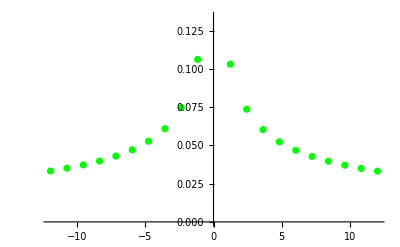

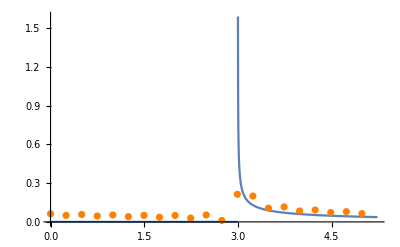

```mathematica
(*First normal without frequency shift*)
ClearAll[bω,b, bT, δt,α]
Maxω=12.; NN= 10; δω=Maxω/NN //N;
(* T=2π NN /Maxω;δt=π/Maxω 2/(2+1/NN);

Print["δω =",δω, ", resulting in time t ∈ Range[0, ",T,",",δt,"]" ];
*)
(*rngω=Range[-Maxω,Maxω,δω];*)
rngω=Range[0,Maxω,δω]; 
  cδ=.3;cδ=.03; δ = cδ δω;
(*rngωFourier=rngω~Join~Reverse@Drop[-rngω,1]+δ;*)
rngωFourier=rngω~Join~Reverse@Drop[-rngω,1]+δ;
 T=2π NN /(Maxω);δt=π/Maxω(2NN)/(2NN+1);

Print["δω =",δω, ", resulting in time t ∈ Range[0, ",T,",",δt,"]" ];

rngt = Range[0,T (2NN)/(2NN+1) ,T/(2NN+1) ];

(*bT=2;δt=.000000001;
α=8;*)
(*b= E^(- α(#-1)^2) (*HeavisideTheta[#-δt]HeavisideTheta[bT-#]  *)&;
bω = (√(2 π))/(√(2 α))E^(- #^2/(4 α))E^(ⅈ #)& ;*)
r0=3.;
b =1/(2π)HeavisideTheta[#-r0]/(√(#^2-r0^2))&;
bω = ⅈ/4 HankelH1[0,# r0]&;

listbOω = bω@rngωFourier;
listbOt= (Sqrt[2 NN+1]/T) Exp[ -ⅈ δ rngt] InverseFourier[listbOω] //Chop; 

lpω= ListPlot[{rngωFourier,Abs@ listbOω}ᵀ(*,{rngω,Abs@ listbOω2}ᵀ}*),PlotStyle->{Orange,Green}]
 pω= Plot[Abs[bω@ω],{ω,-Maxω,Maxω},PlotRange->All];

Show[pω,lpω];
lpt=ListPlot[{rngt,Re@listbOt}ᵀ,PlotStyle->Orange,PlotRange->All];
pt=Plot[Re@b@t,{t,0,T},PlotRange->All];
Show[pt,lpt]
```

```mathematica
rngωFourier=Drop[rngω,1]~Join~Reverse@Drop[-rngω,0]+δ
rngω

rngωFourier=(rngω~Join~Reverse[-rngω])+δ

Reverse[-rngω]
```

{1.2012,2.4012,3.6012,4.8012,6.0012,7.2012,8.4012,9.6012,10.8012,12.0012,-11.9988,-10.7988,-9.5988,-8.3988,-7.1988,-5.9988,-4.7988,-3.5988,-2.3988,-1.1988,0.0012}

{0.,1.2,2.4,3.6,4.8,6.,7.2,8.4,9.6,10.8,12.}

{0.0012,1.2012,2.4012,3.6012,4.8012,6.0012,7.2012,8.4012,9.6012,10.8012,12.0012,-11.9988,-10.7988,-9.5988,-8.3988,-7.1988,-5.9988,-4.7988,-3.5988,-2.3988,-1.1988,0.0012}

{-12.,-10.8,-9.6,-8.4,-7.2,-6.,-4.8,-3.6,-2.4,-1.2,0.}

```mathematica
InverseFourier[listbOω,  FourierParameters -> {1,-1}]
```

{-0.000628759+0.00609671 ⅈ,-0.00596088+0.00451819 ⅈ,-0.000741021+0.00708731 ⅈ,-0.00456795+0.00608491 ⅈ,-0.0000262429+0.00835563 ⅈ,-0.00308866+0.00761685 ⅈ,0.00137332+0.00980406 ⅈ,-0.00126201+0.00917089 ⅈ,0.00357169+0.0114226 ⅈ,0.00115896+0.0107792 ⅈ,0.00692103+0.0132685 ⅈ,0.00456533+0.0124927 ⅈ,0.0122995+0.015547 ⅈ,0.00982501+0.0144582 ⅈ,0.0225043+0.0190513 ⅈ,0.0197944+0.0173027 ⅈ,0.0568674+0.0302084 ⅈ,0.0681288+0.0309735 ⅈ,-0.0141738-0.000857152 ⅈ,0.00144025+0.00586783 ⅈ,-0.00786166+0.00271602 ⅈ}

```mathematica
rngω
```

{0.,1.2,2.4,3.6,4.8,6.,7.2,8.4,9.6,10.8,12.}

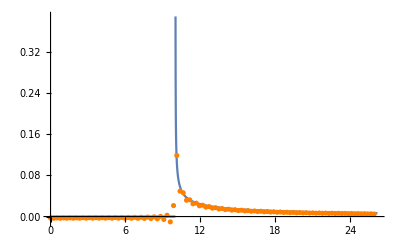
```mathematica
Null^19 -Graphics-
```

### Now for frequency shift with convolution!

```mathematica
ClearAll[b,bω, r0, r] 
(*Maxω=14.; NN= 20; δω=Maxω/NN //N;*)

rs0=0.1;Maxkrs=1.; 
Maxω=Maxkrs/rs0; NN= 45; δω=Maxω/NN //N;
cδ=.3;
(*NN δω == Maxω - cδ δω ⟹*) δω = Maxω /(NN+cδ); 
δ = cδ δω; .13
rngω=Range[0,Maxω-δ,δω];
rngωFourier=rngω~Join~Reverse@Drop[-rngω,1]+δ;

 T=2π NN /(Maxω);δt=π/Maxω(2NN)/(2NN+1);
Print["δω =",δω, ", resulting in time t ∈ Range[0, ",T,",",δt,"]" ];
(*rngω=Range[-Maxω,Maxω,δω];*)
rngt = Range[0,T (2NN)/(2NN+1) ,T/(2NN+1) ];
r=T (NN)/(2NN+1);

g =1/(2π)HeavisideTheta[#-r]/(√(#^2-r^2))&;
gω = ⅈ/4 HankelH1[0,# r]&;

δt=.000000001;
bT=2;b[x_]:=50E^(- 1/(1+δt-(2x/bT -1)^2)) HeavisideTheta[x-δt]HeavisideTheta[bT-x]  ;
bT=  T/(2NN+1);b[x_]:= If[0<= N[x//Chop,4]<= 2 T/(2NN+1),1,0];
Attributes[b]=Listable;

(*α=8; b0 = E^(- α(#-1)^2)&;
b[t_]:= b0[t] E^(ⅈ x δ);
bω = (√(2 π))/(√(2 α))E^(- (#+δ)^2/(4 α))E^(ⅈ (#+δ))&;*)
(*α=2;
b[t_]= E^(- α(t-1)^2) (*HeavisideTheta[#-δt]HeavisideTheta[bT-#]  *);
bω[ω_] = (√(2 π))/(√(2 α))E^(- ω^2/(4 α))E^(ⅈ ω);*)
(*listbOω = bω[rngωFourier];*)
(*
listgOω=T /Sqrt[2NN+1] Fourier[g [rngt] E^(ⅈ rngt δ)];
p1=ListPlot[{rngωFourier,gω[rngωFourier]//Abs }ᵀ,PlotRange-> All, PlotLegends->{"Analytic"}];
p2=ListPlot[{rngωFourier,listgOω//Abs }ᵀ,PlotStyle-> {Orange,PointSize[Large]},PlotRange-> All, PlotLegends->{"Fourier"}];
Show[p1,p2,PlotRange-> All,PlotLabel-> "Compare Frequencies of ĝ"]
*)
listgOt =  (Sqrt[2NN+1]/T) InverseFourier[  gω[rngωFourier] ] E^(-ⅈ rngt δ);
ListPlot[{{rngt,Re@g[rngt]}ᵀ,{rngt,Re@listgOt}ᵀ},PlotRange-> All,PlotLabel-> "Reconstruct g from ĝ"];

(*listbOt =  (Sqrt[2NN+1]/T) InverseFourier[  bω[rngωFourier] ] E^(-ⅈ rngt δ);
ListPlot[{{rngt,Re@b[rngt]}ᵀ,{rngt,Re@listbOt}ᵀ},PlotRange->All]
*)
listgOω = gω[rngωFourier];
listbOω =T /Sqrt[2NN+1] Fourier[b [rngt] E^(ⅈ rngt δ)] ;
listwOt= (Sqrt[2 NN+1]/T) InverseFourier[listbOω listgOω]  E^(-ⅈ rngt δ)//Chop; 
(*listwOt2=T/(2NN+1) (g[rngt]. b[# -rngt])&/@rngt;*)

listgOt =  (Sqrt[2NN+1]/T)Re[ InverseFourier[ listgOω] E^(-ⅈ rngt δ)];
listwOt2= T/(2NN+1)(listgOt. b[#-rngt])&/@rngt;
wFt[t_]:= NIntegrate[ g[τ]b[t-τ],{τ,r,Max[r,t]}];


  lpt=ListPlot[{{rngt,Re@listwOt}ᵀ,{rngt,Re@listwOt2}ᵀ},PlotStyle->{{Orange,PointSize[Large]},{Red,PointSize[Large]}},PlotLegends->{"Frequency sampled w_N^n","Time sampled w_N^n"},PlotRange-> All];         pt =Plot[Re@wFt[t],{t,0,T},PlotRange-> All, PlotLabel->"Convolution of Impluse b(t) with 2D Green's function.",PlotLegends->{"analytic w[t]"},AxesLabel->{"t"}];
 Print@Show[pt,lpt,PlotRange-> All];
```

rngωFourier:{0.0662252,0.286976,0.507726,0.728477,0.949227,1.16998,1.39073,1.61148,1.83223,2.05298,2.27373,2.49448,2.71523,2.93598,3.15673,3.37748,3.59823,3.81898,4.03974,4.26049,4.48124,4.70199,4.92274,5.14349,5.36424,5.58499,5.80574,6.02649,6.24724,6.46799,6.68874,6.90949,7.13024,7.35099,7.57174,7.79249,8.01325,8.234,8.45475,8.6755,8.89625,9.117,9.33775,9.5585,9.77925,10.,-9.86755,-9.6468,-9.42605,-9.2053,-8.98455,-8.7638,-8.54305,-8.3223,-8.10155,-7.88079,-7.66004,-7.43929,-7.21854,-6.99779,-6.77704,-6.55629,-6.33554,-6.11479,-5.89404,-5.67329,-5.45254,-5.23179,-5.01104,-4.79029,-4.56954,-4.34879,-4.12804,-3.90728,-3.68653,-3.46578,-3.24503,-3.02428,-2.80353,-2.58278,-2.36203,-2.14128,-1.92053,-1.69978,-1.47903,-1.25828,-1.03753,-0.816777,-0.596026,-0.375276,-0.154525}

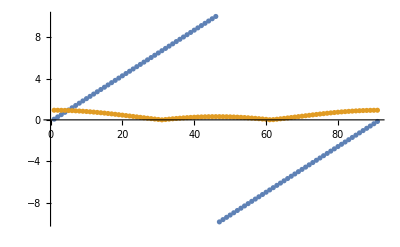

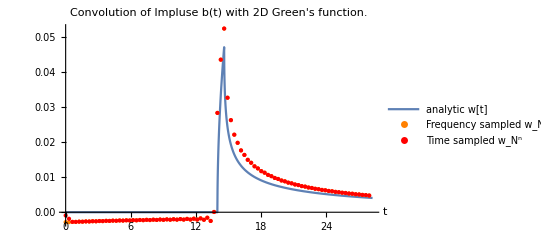

```mathematica
ConvolutionTest[b,T NN/( 2NN+1),rngωFourier]
```

.13

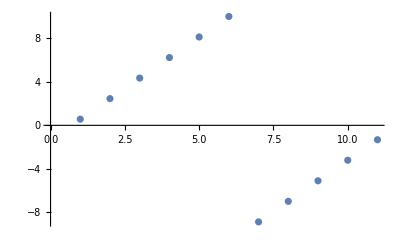

{-8.86792,-6.98113,-5.09434,-3.20755,-1.32075}

{-8.86792,-6.98113,-5.09434,-3.20755,-1.32075}

{-9.86755,-9.6468,-9.42605,-9.2053,-8.98455,-8.7638,-8.54305,-8.3223,-8.10155,-7.88079,-7.66004,-7.43929,-7.21854,-6.99779,-6.77704,-6.55629,-6.33554,-6.11479,-5.89404,-5.67329,-5.45254,-5.23179,-5.01104,-4.79029,-4.56954,-4.34879,-4.12804,-3.90728,-3.68653,-3.46578,-3.24503,-3.02428,-2.80353,-2.58278,-2.36203,-2.14128,-1.92053,-1.69978,-1.47903,-1.25828,-1.03753,-0.816777,-0.596026,-0.375276,-0.154525}

{-9.93377,-9.71302,-9.49227,-9.27152,-9.05077,-8.83002,-8.60927,-8.38852,-8.16777,-7.94702,-7.72627,-7.50552,-7.28477,-7.06402,-6.84327,-6.62252,-6.40177,-6.18102,-5.96026,-5.73951,-5.51876,-5.29801,-5.07726,-4.85651,-4.63576,-4.41501,-4.19426,-3.97351,-3.75276,-3.53201,-3.31126,-3.09051,-2.86976,-2.64901,-2.42826,-2.20751,-1.98675,-1.766,-1.54525,-1.3245,-1.10375,-0.883002,-0.662252,-0.441501,-0.220751}

```mathematica
rngωFourier= {0.06622516556291391,0.2869757174392936,0.5077262693156733,0.728476821192053,0.9492273730684327,1.1699779249448126,1.390728476821192,1.611479028697572,1.8322295805739515,2.0529801324503314,2.273730684326711,2.4944812362030904,2.7152317880794703,2.9359823399558502,3.1567328918322297,3.377483443708609,3.598233995584989,3.818984547461369,4.039735099337749,4.260485651214128,4.481236203090508,4.701986754966888,4.922737306843267,5.143487858719647,5.364238410596027,5.584988962472407,5.805739514348787,6.026490066225166,6.247240618101546,6.467991169977926,6.688741721854305,6.9094922737306845,7.1302428256070645,7.350993377483444,7.571743929359824,7.792494481236203,8.013245033112584,8.233995584988962,8.454746136865342,8.675496688741722,8.896247240618102,9.116997792494482,9.337748344370862,9.558498896247242,9.77924944812362,10.,-9.933774834437086,-9.713024282560706,-9.492273730684326,-9.271523178807946,-9.050772626931566,-8.830022075055188,-8.609271523178808,-8.388520971302428,-8.167770419426049,-7.947019867549669,-7.726269315673289,-7.50551876379691,-7.28476821192053,-7.06401766004415,-6.843267108167771,-6.622516556291391,-6.401766004415011,-6.181015452538631,-5.960264900662251,-5.739514348785872,-5.518763796909492,-5.298013245033112,-5.077262693156733,-4.856512141280353,-4.635761589403973,-4.415011037527593,-4.194260485651213,-3.9735099337748343,-3.7527593818984544,-3.5320088300220744,-3.3112582781456954,-3.0905077262693155,-2.8697571743929355,-2.6490066225165556,-2.4282560706401757,-2.2075055187637966,-1.9867549668874167,-1.7660044150110377,-1.5452538631346577,-1.3245033112582778,-1.1037527593818979,-0.8830022075055178,-0.6622516556291379,-0.441501103752758,-0.22075055187637982};

Maxkrs=1.; 
Maxω=Maxkrs/rs0; NN= 5; δω=Maxω/NN //N;
cδ=.3;
(*NN δω == Maxω - cδ δω ⟹*) δω = Maxω /(NN+cδ); 
δ = cδ δω; .13
rngω=Range[0,Maxω-δ,δω];
rngωFourier2=rngω~Join~Reverse@Drop[-rngω,1]+δ;
ListPlot[rngωFourier2]
Reverse@Drop[-rngω,1] +δ
Range[-Maxω+δ, -δω, δω]   +δ
```

```mathematica
First@rngωFourier
First@rngωFourier2
(Length[rngωFourier]-1)/2
(Length[rngωFourier2]-1)/2
Max@rngωFourier
Max@rngωFourier2

rngωFourier-rngωFourier2
```

0.0662252

0.0662252

45

45

10.

10.

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252,-0.0662252}

rngωFourier:{0.0662252,0.286976,0.507726,0.728477,0.949227,1.16998,1.39073,1.61148,1.83223,2.05298,2.27373,2.49448,2.71523,2.93598,3.15673,3.37748,3.59823,3.81898,4.03974,4.26049,4.48124,4.70199,4.92274,5.14349,5.36424,5.58499,5.80574,6.02649,6.24724,6.46799,6.68874,6.90949,7.13024,7.35099,7.57174,7.79249,8.01325,8.234,8.45475,8.6755,8.89625,9.117,9.33775,9.5585,9.77925,10.,-9.93377,-9.71302,-9.49227,-9.27152,-9.05077,-8.83002,-8.60927,-8.38852,-8.16777,-7.94702,-7.72627,-7.50552,-7.28477,-7.06402,-6.84327,-6.62252,-6.40177,-6.18102,-5.96026,-5.73951,-5.51876,-5.29801,-5.07726,-4.85651,-4.63576,-4.41501,-4.19426,-3.97351,-3.75276,-3.53201,-3.31126,-3.09051,-2.86976,-2.64901,-2.42826,-2.20751,-1.98675,-1.766,-1.54525,-1.3245,-1.10375,-0.883002,-0.662252,-0.441501,-0.220751}

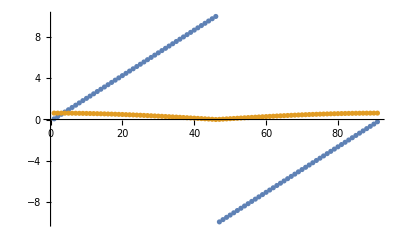

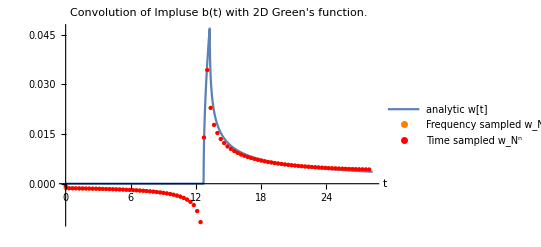

```mathematica
ConvolutionTest[b,T NN/( 2NN+1),rngωFourier]
```